# MGDrivE: MCR Analysis

## 0) Functions

```mathematica
<<colorBlender`
SetDirectory[NotebookDirectory[]];
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
AddLabelsToReshapedDataNode[reshapedDataNode_,genotypes_,patchNumber_]:=Module[{breakdownWithPop,breakdownWithTime,labels},
breakdownWithPop=Prepend[#,patchNumber]&/@reshapedDataNode[[All,2;;All]];
breakdownWithTime=Prepend[#[[2]],#[[1]]]&/@Transpose[{Range[breakdownWithPop//Length],breakdownWithPop}];
labels=Prepend[ReplacePart[genotypes,1->"Patch"],"Time"];
Prepend[breakdownWithTime,labels]
]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,3;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Gray]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->40,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]


ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
Yellow,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+2*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+2*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{ImageRotate[barChart,90Degree]//Show[#]&,dayCount//Show[#]&,network//Show[#]&,popCount//Show[#]&,ImageRotate[flow,90Degree]//Show[#]&}}];
Rasterize[row]
]
GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_},ticks_]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicks->ticks,
FrameTicksStyle->17.5,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
AxesLabel->(Style[#,40]&/@{"Time","Genotype Breakdown"}),
BarSpacing->{0,0},
AspectRatio->1/3,
PlotRangePadding->{0,0},
BarOrigin->Bottom,
ImageSize->1000(*frameDimensions[[1]]*) ,
Epilog->Flatten[{Lighter[Gray,.5],Thickness[.0005],Opacity[.5],(Line[{{#,0},{#,maxPop}}]&/@Range[0,ticksMax,250]),(Line[{{0,#},{ticksMax,#}}]&/@Range[0,maxPop,1000])}]
]
]
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_,tag_]:=Module[{plotRight,plotLeft},
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameTicksStyle->Directive[Gray,18],
FrameLabel->(Style[#,40]&/@plotLabels),
Epilog->Style[Text[tag,{900,550}],Directive[Gray,35]]
]
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
```

## 1) Single Experiment Dynamics

Load Data

```mathematica
(*Experiment name = folder name*)
experimentName="Invasiveness_MCR_090318/MCR_LINE/2018_09_03_ANALYZED/";
experimentString="MCRLine";
timeRange={1,365*2//Round};
releasesStart=0;
(**)
directoryData=Directory[]<>"/"<>experimentName<>"/";
experimentFolders=directoryData
(**)
cellFolder=experimentFolders;
releaseTimes={releasesStart,(1*7)+releasesStart};
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
(**)
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
```

/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_MCR_090318/MCR_LINE/2018_09_03_ANALYZED//

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
WW | WH | WR | WB | WY | HH | HR | HB | HY | RR | RB | RY | BB | BY

Aggregate Data By Genotype

```mathematica
genotypesGroups={
{{2,6,6,7,8,9},"H"},
{{1,1,2,3,4,5},"W"},
{{3,10,10,11,12},"R"},
{{4,8,11,13,13},"B"}
};
(*Aggregate by group*)
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
aggregatedGroupData=transposedTotals;
```

Define Color Palette

```mathematica
originalColorsValues={
{0,100,70,0},
{70,50,0,0},
{50,100,0,0},
{0,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Transpose[{rgbColors,genotypesGroups[[All,2]]}]//Grid;
maxPopSize=aggregatedGroupData//Flatten//Max;
SwatchLegend[rgbColors,genotypesGroups[[All,2]]
,LabelStyle->30
,LegendMarkerSize->25
]
Export["./images/MCR/"<>"_03.png",%,ImageResolution->500];
```

Plot

### Normalized

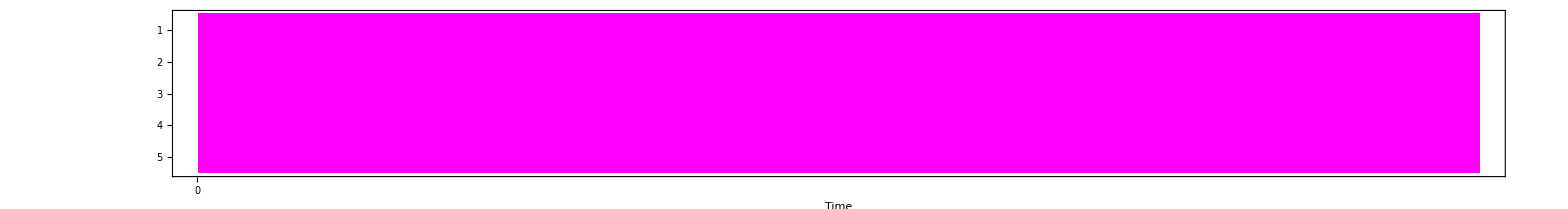

./images/MCR/MCRLine_01A.png

```mathematica
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
(**)
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots;
Show[matrixPlots]
Export["./images/MCR/"<>experimentString<>"_01A.png",%,ImageSize->5000]
```

### Normalized Split

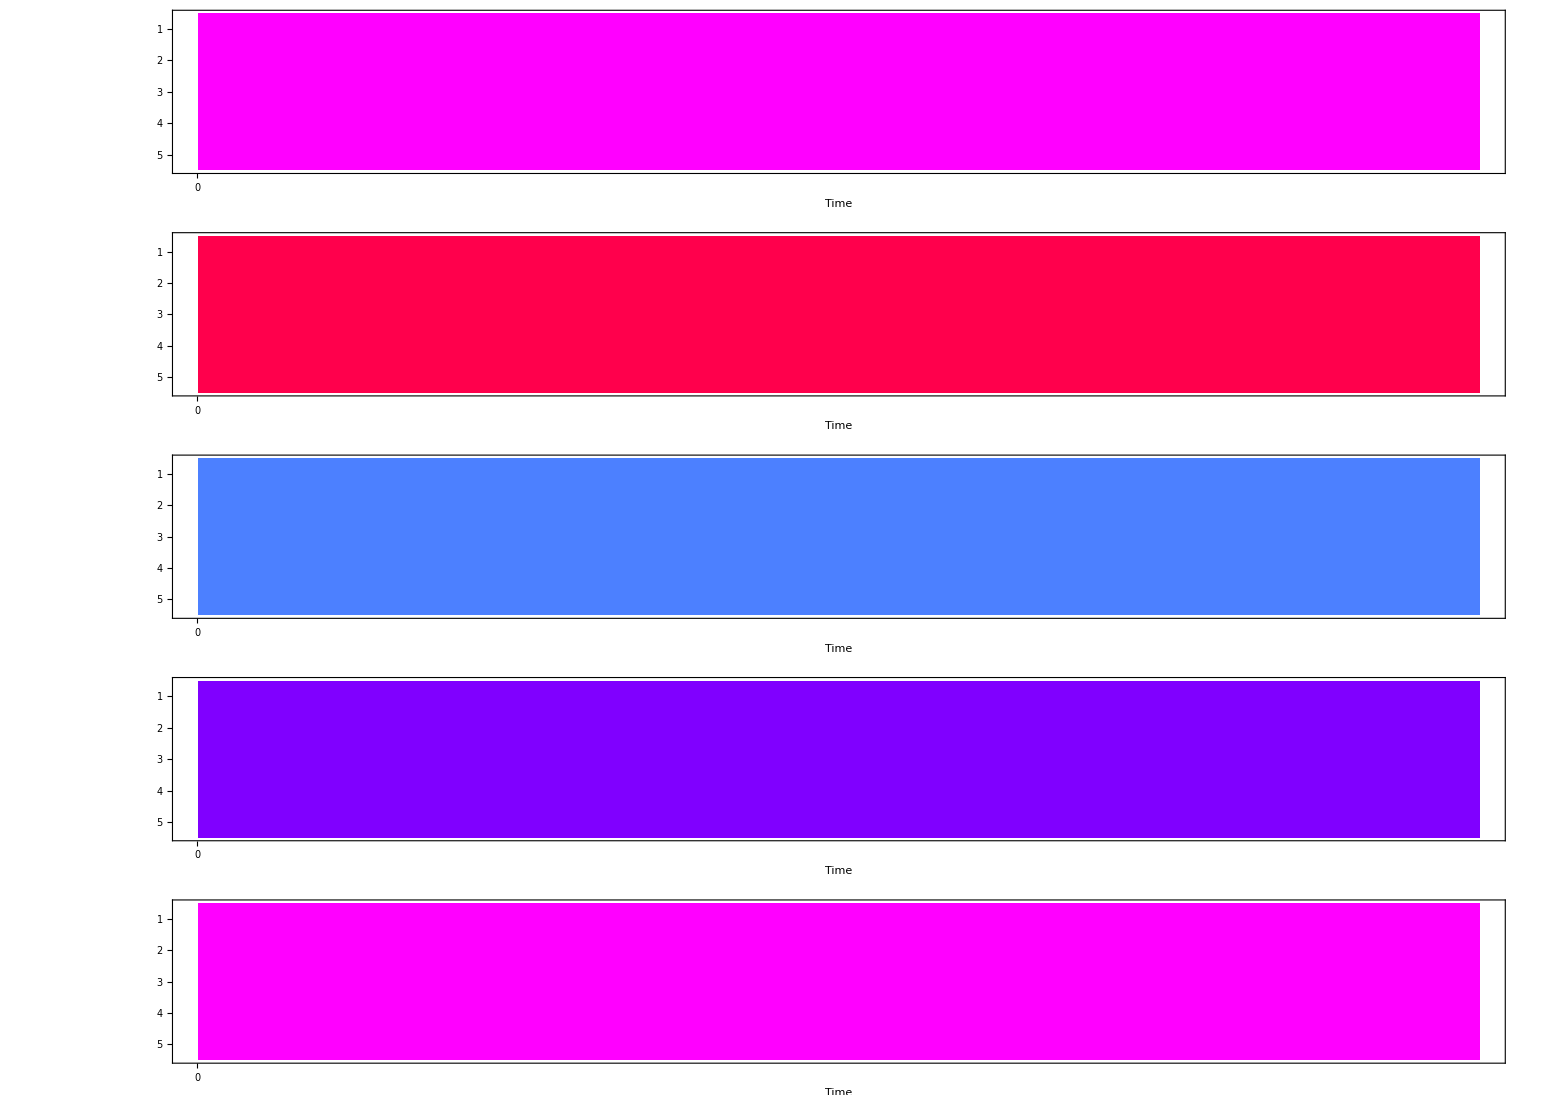

./images/MCR/MCRLine_01C.png

```mathematica
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
(**)
aspectRatio=10;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.001],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,.00001],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,.00001]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.25*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
Show[matrixPlots];
GraphicsGrid[Prepend[Transpose[{matrixPlots}],{Show[matrixPlots]}]]
Export["./images/MCR/"<>experimentString<>"_01C.png",%,ImageSize->5000]
```

### Un-Normalized

```mathematica
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.0025]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},2*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
Show[matrixPlots]
Export["./images/MCR/"<>experimentString<>"_01B.png",%,ImageSize->5000]
```

-Graphics-

./images/MCR/MCRLine_01B.png

### BarChart

```mathematica
counts=ParallelTable[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}];
```

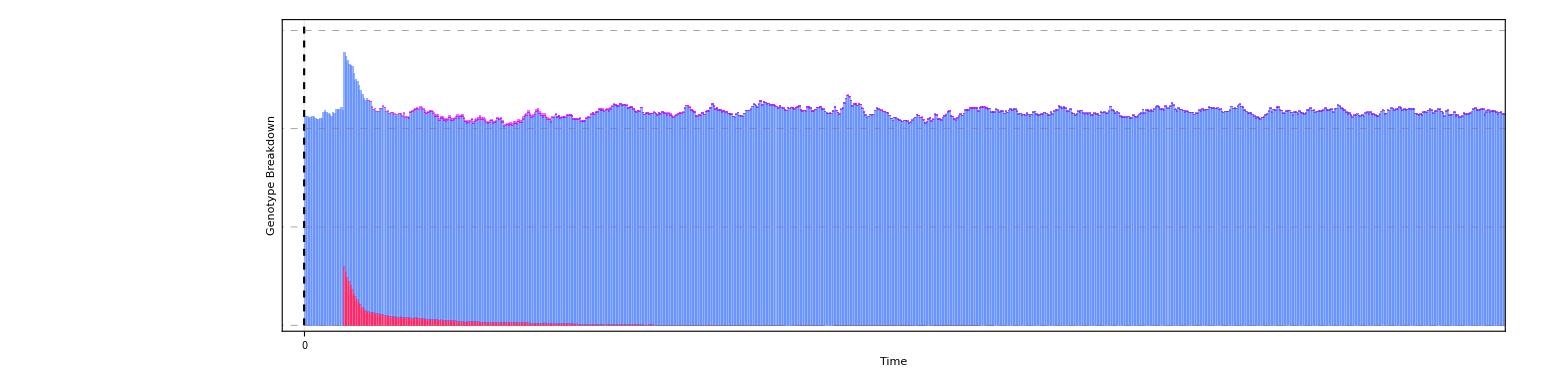

./images/MCR/MCRLine_02.png

```mathematica
BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,50],Range[0,1.5*counts//Flatten//Max,50]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],365*2},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
Export["./images/MCR/"<>experimentString<>"_02.png",%,ImageSize->2500]
```